TTTR fluorescence data simulations for diffusing particles

Simulation in three stepspaclet:Fretica/tutorial/TTTRFluorescenceDataSimulationsForDiffusingParticles#323930723 | Example 3: FRET-labeled system with state-kinetics paclet:Fretica/tutorial/TTTRFluorescenceDataSimulationsForDiffusingParticles#48523463
Diffusion through the laser focuspaclet:Fretica/tutorial/TTTRFluorescenceDataSimulationsForDiffusingParticles#328673729 | Example 4: FRET-labeled system with photo bleachingpaclet:Fretica/tutorial/TTTRFluorescenceDataSimulationsForDiffusingParticles#579858115
Example 1: Mixture of species with D_1=5 D_2, no internal states, labeled with different dyes paclet:Fretica/tutorial/TTTRFluorescenceDataSimulationsForDiffusingParticles#37005626 | Example 5: FRET-labeled system with lifetime-information and PIEpaclet:Fretica/tutorial/TTTRFluorescenceDataSimulationsForDiffusingParticles#598341287
Example 2: FRET-labeled system (static)paclet:Fretica/tutorial/TTTRFluorescenceDataSimulationsForDiffusingParticles#1035056785 |

TTTR = Time Tagged Time-Resolved

### Preliminaries

```mathematica
Needs["Fretica`"]
```

Build time: Jun 27 2022  10:54:05

```mathematica
SetDirectory[$FreticaExamples]
```

W:\Work\Retreat Les Diablerets

#### Definitions

```mathematica
sim2D[R_,Tmax_][r0:{_,_}]:=Module[{diff=0.02,r=r0,dr,t=0},
dr:=RandomVariate[NormalDistribution[0,2 diff]];
Reap[
While[Norm[r]<R && t<Tmax, 
Sow[r];
r+={dr,dr};
t++;]

][[2,1]]
]
```

Simulation in three steps

Diffusion through the laser focus
(FTSSimulateParticleDiffusion)

Internal-state dynamics, define photon rates
(FTSSimulateStateTrajectories or  FTSSimulateTTTRLifeTimes)

Photon emission
(FTSSimulateTTTR, FTSSimulateTTTRLifeTimes)

Diffusion through the laser focus

### Simulation of particles diffusing in an open sphere

Goal:
Realistic simulation of a very dilute heterogenous mixture of particles through the confocal volume with defined concentrations of every subpopulation.

Problem: 
In a closed simulation space, the volume must be large enough that at least one molecule is present of each species. At the same time the correct concentrations off all subpopulations must be matched.
⟹ Potentially, many particles need to be simulated in a large space, although the confocal volume is tiny and empty most of the time.

Solution:
– Simulation in a open sphere of moderate size (radius R). 
– The simulation is started with a random distribution of particles. 
– Each trajectory is simulated until the particle leaves the sphere.
– To compensate the losses, new particles appear periodically in time intervals T_new near the edge of the sphere.

⟹ Even tiny subpopulations are realized while only a small volume around the confocal volume needs to be simulated.

### Particle concentrations decreases at the edge of the sphere, but remains constant at the center, if T_new is small enough.

```mathematica
pts=RandomPoint[Disk[{0,0},4],1000];
traj=sim2D[4,800]/@pts;
traj2=Flatten[traj,{{2},{1}}];
ListAnimate[Map[ListPlot[#,PlotRange->{{-4.1,4.1},{-4.1,4.1}},PlotStyle->PointSize[Medium],Prolog->{ Circle[{0,0},4],Green,Disk[{0,0},{0.3,1}],Gray,Line[{{0,1},{0,0},{0.3,0}}]},AspectRatio->1,Axes->False]&,traj2[[1;;800;;2]]]]
```

### The loss of particles is compensated periodically.

```mathematica
simcartoon[t_]:=Module[{Tnew=50,Tmax=200},GraphicsRow[{Show[DensityPlot[1-FTSNewParticleConcentration[4,0.005,1,Sqrt[x^2+y^2],t- Tnew Floor[t/Tnew]],{x,-4,4},{y,-4,4},ColorFunction->(Opacity[#,Lighter@Lighter@Blue]&),Frame->False],Graphics[{ Circle[{0,0},4],Green,Disk[{0,0},{0.3,1}],Gray,Line[{{0,1},{0,0},{0.3,0}}]}],ImageSize->300],
Plot[1,{t1,00.1,t},PlotRange->{{0,Tmax},{0,2}},Ticks->{{{0,0},{Tnew,"T_new"},{2Tnew,"2T_new"},{3Tnew,"3T_new"}},None},AspectRatio->0.2,Epilog->{Red,Table[Line[{{i*Tnew,0},{i*Tnew,2}}],{i,3}]}]}]
]
mov=Table[
simcartoon[t]
,{t,0,200,5}];
ListAnimate[mov]
```

### To save memory, only trajectories with T>T_min which come close enough to the confocal volume (r<R_Save) are kept in memory.

```mathematica
pts=RandomPoint[Disk[{0,0},4],4000];
pts=Select[pts,Norm[#]>3.5&];
traj=sim2D[4,800]/@pts;
ListPlot[traj,PlotRange->{{-4.1,4.1},{-4.1,4.1}},Joined->True,Prolog->{ Circle[{0,0},4],Green,Disk[{0,0},{0.3,1}],Gray,Line[{{0,1},{0,0},{0.3,0}}]},Epilog->{AbsoluteThickness[2],Circle[{0,0},1.5],Text[Style["R_Save",Large],{1.5,1.5}]},AspectRatio->1,Axes->False]
```

-Graphics-

### Simulation modes

“1D”
Only the radial distance r=√(x^2+y^2+z^2) is simulated and saved (default)

“2D”
Only ρ=√(x^2+y^2) and z are simulated and saved

### Fretica commands

```mathematica
?FTSSetNumberOfSpecies
```

```mathematica
?FTSSimulateParticleDiffusion
```

## Examples

Example 1: Mixture of species with D_1=5 D_2, no internal states, labeled with different dyes

#### Parameters

```mathematica
FTSSetNumberOfSpecies[2];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.5;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;


diff1=0.0001;(* μm^2/μs *)
c1=30. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)

diff2=0.00002;(* μm^2/μs *)
c2=30. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.4;z0=1.; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
```

0.890932

#### T_new cycle

```mathematica
4/3 π Rsphere^3 c1
FTSMeanNewParticleNumberInSphere[Rsphere,diff1,c1,Tnew]
```

2.04322

FTSMeanNewParticleNumberInSphere[3.,0.0001,0.018066,1000]

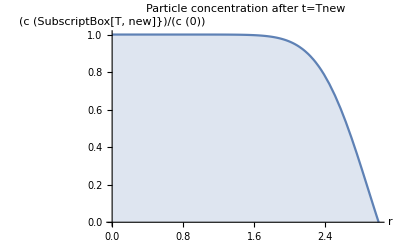

```mathematica
Plot[1-FTSNewParticleConcentration[Rsphere,diff1,c1,r,dt*Tnew]/c1,{r,0,Rsphere},Frame->False,Filling->Bottom,PlotLabel->"Particle concentration after t=Tnew",PlotRange->All,AxesLabel->{"r","(c (SubscriptBox[T, new]})/(c (0))"}]
```

#### Simulation of r-trajectories

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"2D"]//AbsoluteTiming
```

{60.288,41536}

```mathematica
FTSSimulateParticleDiffusion[2,Rsphere,diff2,c2,T,dt,Tnew,Tmin,Rsave,Method->"2D"]//AbsoluteTiming
```

{107.497,8368}

```mathematica
sim=FTSGetTrajectories[1,1;;25,3.,10];
ListPlot[Select[FTSDistanceTrajectory[sim],UnsameQ[#,{}]&],PlotLabel->"Species 1",AxesLabel->{"time(sec)", "r (μm)"}]
```

-Graphics-

```mathematica
sim=FTSGetTrajectories[2,1;;3,3.,10];
ListPlot[Select[FTSDistanceTrajectory[sim],UnsameQ[#,{}]&],PlotLabel->"Species 2",AxesLabel->{"time(sec)", "r (μm)"}]
```

-Graphics-

#### Set photon rates

The photon rate depends on the particle’s position in the confocal volume.
Typically the dependence is described by a 3D Gaussian:

n(r)=n(x,y,z)=n_0 exp((-2(x^2+y^2))/w_0^2)exp((-2 z^2)/z_0^2)

```mathematica
w0=.4;z0=1.; (*μm*)
Veff=π^(3/2)w0^2 z0  (*volume of confocal volume*)
Neff=Veff c1 (* mean particle number in confocal volume*)
```

0.890932

0.0160956

Define photon rates at the center of the confocal volume  for each channel :

```mathematica
n01={1.,0}; (*counts/μs,  species 1*)
n02={0,2.}; (*counts/μs, species 2*)

FTSSimulateStateTrajectories[{1,{n01},{1}}];
FTSSimulateStateTrajectories[{2,{n02},{1}}];
```

#### Simulate photons

```mathematica
rmax=2.; (*up to this distance particle can contribute photons*)
```

```mathematica
Exp[-2 rmax^2/z0^2]
```

0.000335463

```mathematica
bg1=0;  (* background rate on detection channel 1 *)
bg2=0 ; (* background rate on detection channel 2 *)
```

```mathematica
AbsoluteTiming[FTSSimulateTTTR[{bg1,bg2},rmax,w0,z0]]
```

{27.2925,1}

```mathematica
(*FSaveAsHT3["Simulation example 1.ht3"]*)
```

1

```mathematica
FOpenTTTR["Simulation example 1.ht3"]
```

#### Photon Traces (MCS traces)

```mathematica
FMCStrace[{{1,0},{0,1}},1,0,5]
```

-Graphics-

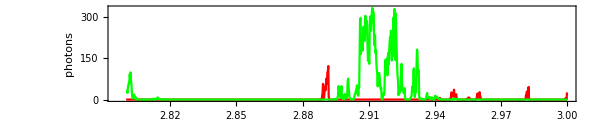

```mathematica
FMCStrace[{{1,0},{0,1}},0.2,2.8,3]
```

#### FCS

{27.429,1}

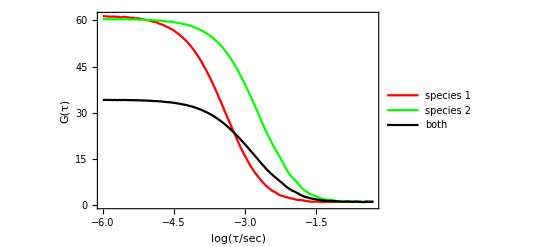

```mathematica
AbsoluteTiming[FTSSimulateTTTR[{0,0},2.0,w0,z0]]
Show[FFCSW[-5.9,0.,{1,0,0,0},{1,0,0,0},FOutput->FGraph,PlotStyle->Red],
FFCSW[-5.9,0.,{0,1,0,0},{0,1,0,0},FOutput->FGraph,PlotStyle->Green],
FFCSW[-5.9,0.,{1,1,0,0},{1,1,0,0},FOutput->FGraph,PlotStyle->Black],Graphics[Inset[LineLegend[{Red,Green,Black},{"species 1","species 2","both"}],Scaled@{.8,.8}]]]
```

```mathematica
1+1/Neff
```

63.1288

#### PCH

```mathematica
FPCH[{{1,0,0,0},{0,1,0,0}},0.2,PlotStyle->{Red,Green}]
```

-Graphics-

Example 2: FRET-labeled system (static)

#### Simulation r-trajectories

```mathematica
FTSSetNumberOfSpecies[1];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.0;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;
diff1=0.00005;(* μm^2/μs *)
c1=50. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.5;z0=0.5; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
Neff=Veff c1
```

0.696041

0.0209578

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"1D"]//AbsoluteTiming
```

{69.074,17378}

#### Set photon rates for three states (D, U, N)

correction factors:

```mathematica
γ=1.5; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
rcm:=({{1, -ct}, {0, γ}});
```

photon rates:

```mathematica
ntot=0.2 (* photons/μs*) (* at center laser focus*)
eD=0;eU=0.5;eN=0.95; (* transfer efficiencies *)

(*photon rates of ideal instrument and dyes*)
nD=ntot {eD,(1-eD)};
nU=ntot {eU,(1-eU)};
nN=ntot {eN,(1-eN)};

(*photon rates of real instrument and dyes*)
invrcm=Inverse[rcm];
nD=invrcm.nD;
nU=invrcm.((1-α)nU+α ntot{1,0});
nN=invrcm.((1-α)nN+α ntot{1,0});
```

0.2

```mathematica
p0={pD=0.5,pU=1,pN=1}; (* relative populations *)
FTSSimulateStateTrajectories[{1,{nD,nU,nN},p0}]
```

1

#### Simulate photons

```mathematica
rmax=1; (* up to rmax fluorescence rate ist calculated*)
nbgA=  0.0015;
nbgD=   0.003;
AbsoluteTiming[FTSSimulateTTTR[{nbgA,nbgD},rmax,w0,z0]]
```

{11.6466,1}

```mathematica
(*FSaveAsHT3["Simulation example 2.ht3"]*)
```

1

```mathematica
FOpenTTTR["Simulation example 3.ht3"]
```

#### Photon Traces (MCS traces)

```mathematica
FMCStrace[{{1,0},{0,1}},1,0,5]
```

-Graphics-

#### FCS

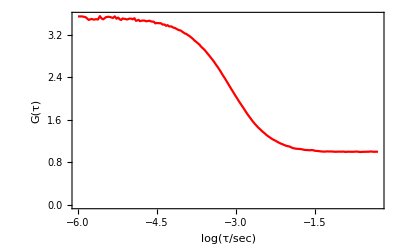

```mathematica
FFCSW[-5.9,0.,{1,1},{1,1},FOutput->FGraph,PlotStyle->Red]
```

```mathematica
1+1/Neff
```

48.7149

#### PCH

```mathematica
FPCH[{{1,0,0,0},{0,1,0,0}},0.2,PlotStyle->{Red,Green}]
```

-Graphics-

#### Burst identification

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
```

```mathematica
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,20,10000];
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000]
```

{1697.36,3099.89,0.,0.,0.,0.}

4195

#### Transfer efficiency histogram

```mathematica
fit=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{0,0.55,0.9}];
fit[[2]]
```

General::munfl: Exp[-812.487] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
{Pos[1],Pos[2],Pos[3]}/.fit[[1]]
pop=FFRETPeakIntegrate[{"G","G","G"},fit[[1]],{-0.2,1.2}];pop/=Total[pop]
```

{0.0271029,0.612675,0.961686}

{0.157061,0.396242,0.446697}

Example 3: FRET-labeled system with state-kinetics

#### Simulation r-trajectories

```mathematica
FTSSetNumberOfSpecies[1];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.0;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;
diff1=0.00005;(* μm^2/μs *)
c1=50. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.5;z0=0.5; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
Neff=Veff c1
```

0.696041

0.0209578

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"1D"]//AbsoluteTiming
```

{64.7785,17362}

#### Set photon rates for three states (D, U, N)

correction factors:

```mathematica
γ=1.5; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
rcm:=({{1, -ct}, {0, γ}});
```

photon rates:

```mathematica
ntot=0.2 (* photons/μs*) (* at center laser focus*)
eD=0;eU=0.5;eN=0.95; (* transfer efficiencies *)

(*photon rates of ideal instrument and dyes*)
nD=ntot {eD,(1-eD)};
nU=ntot {eU,(1-eU)};
nN=ntot {eN,(1-eN)};

(*photon rates of real instrument and dyes*)
invrcm=Inverse[rcm];
nD=invrcm.nD;
nU=invrcm.((1-α)nU+α ntot{1,0});
nN=invrcm.((1-α)nN+α ntot{1,0});
```

0.2

#### Simulate state dynamics (U ⇌ N)

```mathematica
kf=0.001;ku=0.001 ; (*1/μs*)
pDonly=0.2;
Km=({{0, 0, 0}, {0, -kf, ku}, {0, kf, -ku}});
p0={pDonly,(1-pDonly)ku/(kf+ku),(1-pDonly)kf/(kf+ku)};
FTSSimulateStateTrajectories[{1,{nD,nU,nN},p0,Km}];
```

#### Simulate photons

```mathematica
rmax=1; (* up to rmax fluorescence rate ist calculated*)
nbgA=  0.0015;
nbgD=   0.003;
AbsoluteTiming[FTSSimulateTTTR[{nbgA,nbgD},rmax,w0,z0]]
```

{11.1675,1}

```mathematica
(*FSaveAsHT3["Simulation example 3.ht3"]*)
```

1

```mathematica
FOpenTTTR["Simulation example 3.ht3"]
```

#### Burst identification

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
```

```mathematica
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,20,10000];
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000]
```

{1675.51,3064.6,0.,0.,0.,0.}

4728

#### Transfer efficiency histogram

```mathematica
fit=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{0,0.5,0.9}];
fit[[2]]
```

-Graphics-

Example 4: FRET-labeled system with photo bleaching

#### Simulation r-trajectories

```mathematica
FTSSetNumberOfSpecies[1];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.0;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;
diff1=0.00005;(* μm^2/μs *)
c1=50. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.5;z0=0.5; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
Neff=Veff c1
```

0.696041

0.0209578

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"1D"]//AbsoluteTiming
```

{64.8242,17495}

#### Set photon rates for four states ( D, U, N, A )

correction factors:

```mathematica
γ=1.5; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
rcm:=({{1, -ct}, {0, γ}});
```

photon rates:

```mathematica
ntot=0.2 (* photons/μs*) (* at center laser focus*)
eD=0;eU=0.5;eN=0.95; (* transfer efficiencies *)

(*photon rates of ideal instrument and dyes*)
nD=ntot {eD,(1-eD)};
nU=ntot {eU,(1-eU)};
nN=ntot {eN,(1-eN)};
nA={0,0};

(*photon rates of real instrument and dyes*)
invrcm=Inverse[rcm];
nD=invrcm.nD;
nU=invrcm.((1-α)nU+α ntot{1,0});
nN=invrcm.((1-α)nN+α ntot{1,0});
nA=invrcm.(α ntot{1,0});
```

0.2

#### Simulate state dynamics ( bleaching)

```mathematica
kf=0;ku=0 ; (*1/μs*)
kabl=0.0003;
kdbl=0.00004;
Km=({{0, 0, 0, 0}, {0, -kf, ku, 0}, {0, kf, -ku, 0}, {0, 0, 0, 0}});
Kbleach=({{0, kabl (eU), kabl (eN), 0}, {0, -kabl (eU) -kdbl (1-eU), 0, 0}, {0, 0, -kabl (eN)-kdbl(1-eN), 0}, {0, kdbl (1-eU), kdbl (1-eN), 0}});
p0={0.1,0.4,0.4,0.1};
```

```mathematica
rmax=1; (* up to rmax fluorescence rate ist calculated*)
AbsoluteTiming[FTSSimulateStateTrajectories[{1,{nD,nU,nN,nA},p0,Km,Kbleach},w0,z0,rmax]]
```

{7.05061,1}

#### Simulate photons

```mathematica
nbgA=  0.0015;
nbgD=   0.003;
AbsoluteTiming[FTSSimulateTTTR[{nbgA,nbgD},rmax,w0,z0]]
```

{11.8754,1}

```mathematica
(*FSaveAsHT3["Simulation example 4.ht3"]*)
```

1

```mathematica
FOpenTTTR["Simulation example 4.ht3"]
```

#### Burst identification

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
```

```mathematica
FDetermineBackground[];
FFindBurstsDeltaT[0.00015,20,10000];
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000]
```

{1674.92,3061.89,0.,0.,0.,0.}

4275

#### Transfer efficiency histogram

```mathematica
fit=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{0,0.5,0.9}];
fit[[2]]
```

-Graphics-

```mathematica
FCutAsymmetricBursts[2.];
fit=FFitFretHistogram[{-0.2,1.2,0.02},{"G","G","G"},{0,0.5,0.9}];
fit[[2]]
```

-Graphics-

Example 5: FRET-labeled system with lifetime-information and PIE

### Simulation r-trajectories

```mathematica
FTSSetNumberOfSpecies[1];
```

```mathematica
Rsphere=3.;(* μm *)
T=600 10^6; (* μs *)
dt=1.; (*time between simulation steps in μs *)
Tnew=1000;(* in units of dt *)
Tmin=1;(* in units of dt *)
Rsave=1.0;
PicoMolarToParticlesPerFemtoliter=10^-12 10^-15 6.022 10^23;
diff1=0.00005;(* μm^2/μs *)
c1=50. * PicoMolarToParticlesPerFemtoliter; (* #particle/femtoliter*)
```

```mathematica
w0=.5;z0=0.5; (*μm*)
Veff=π^(3/2)w0^2 z0  (*femtoliter*)
Neff=Veff c1
```

0.696041

0.0209578

```mathematica
FTSSimulateParticleDiffusion[1,Rsphere,diff1,c1,T,dt,Tnew,Tmin,Rsave,Method->"1D"]//AbsoluteTiming
```

{68.5869,17526}

### Set up photon rates

correction factors:

```mathematica
γ=1.2; (*correcting for unequal quantum yields and detection efficienies*)
ct=0.08; (*cross talk, i.e. leakage of donor photons into acceptor detection channel*)
α=0.04; (*acceptor direct excitation*)
G=0.95;
rcm=({{1, -ct, 0, 0}, {0, γ, 0, 0}, {0, 0, G, -G ct}, {0, 0, 0, G γ}});
invrcm=Inverse[rcm];

pieγ= 1.2;
```

photon rates:

```mathematica
Clear[ip,is,itot]
Solve[{(ip-is)/(ip+2is)==r,itot==ip+is},{ip,is}]//Simplify
```

{{ip→(itot+2 itot r)/(2+r),is→(itot-itot r)/(2+r)}}

```mathematica
n4decays[{ntot_,e_,rd_,ra_,α_}][{idap_,iddp_,idas_,idds_,iaap_,iaas_}(*normalized decays*)]:=ntot(1-α){1/2e idap,(1-e)(1+2rd)/(2+rd)iddp,1/2e idas,(1-e)(1-rd)/(2+rd)idds}+ntot α{(1+2ra)/(2+ra)iaap,0,(1-ra)/(2+ra)iaas,0}
```

```mathematica
Clear[GetSubpopDecays]
GetSubpopDecays[{ntot_,e_,rd_,ra_,α_,pieγ_},Dexdecays:{idap_,iddp_,idas_,idds_,idirap_,idiras_,idonlyp_,idonlys_},Aexdecays:{iaap_,iaas_}]:=Module[
{
nDexDonly=n4decays[{ntot,0,rd,0,0}][{idonlyp,idonlyp,idonlys,idonlys,idonlyp,idonlyp}],
nDexFRET=n4decays[{ntot,e,rd,ra,α}][Dexdecays[[1;;6]]],
nDexAonly=n4decays[{α ntot,0,0,ra,1}][Dexdecays[[1;;6]]],

nAexDonly=0 {iaap,iaap,iaap,iaap},
nAexFRET=ntot {(1+2ra)/(2+ra)iaap,0 iaap,(1-ra)/(2+ra)iaas,0 iaas},
nAexAonly=ntot {(1+2ra)/(2+ra)iaap,0 iaap,(1-ra)/(2+ra)iaas,0 iaas},
nDonly,nFRET,nAonly
},

nDonly=invrcm.nDexDonly+nAexDonly/pieγ; 
nFRET=invrcm.nDexFRET+nAexFRET/pieγ; 
nAonly=invrcm.nDexAonly+nAexAonly/pieγ; 


{nDonly,nFRET,nAonly}
]
```

```mathematica
ntotfree=0.4; ntotbound=0.4; (* photons/μs at center laser focus*)
efree=0.5;ebound=0.8; (* transfer efficiencies *)
rDfree=0.04; rDbound=0.12; (* steady state anisotropies *)
rAfree=0.04; rAbound=0.12;

nfree=GetSubpopDecays[{ntotfree,efree,rDfree,rAfree,α,pieγ},{1,1,1,1,1,1,1,1},{1,1}]
nbound=GetSubpopDecays[{ntotbound,ebound,rDbound,rAbound,α,pieγ},{1,1,1,1,1,1,1,1},{1,1}]
```

{{0.0141176,0.176471,0.0132095,0.165119},{0.287718,0.0847059,0.272182,0.079257},{0.184941,0.,0.164788,0.}}

{{0.0155975,0.194969,0.0116518,0.145647},{0.360922,0.037434,0.309277,0.0279643},{0.204327,0.,0.145356,0.}}

```mathematica
ntot={nfree[[1]],nfree[[2]],nbound[[2]],nbound[[3]]}
```

{{0.0141176,0.176471,0.0132095,0.165119},{0.287718,0.0847059,0.272182,0.079257},{0.360922,0.037434,0.309277,0.0279643},{0.204327,0.,0.145356,0.}}

#### Simulate state dynamics ( bleaching)

```mathematica
kf=0;ku=0 ; (*1/μs*)
kabl=0.0003;
kdbl=0.00004;
Km=({{0, 0, 0, 0}, {0, -kf, ku, 0}, {0, kf, -ku, 0}, {0, 0, 0, 0}});
Kbleach=({{0, kabl (eU), kabl (eN), 0}, {0, -kabl (eU) -kdbl (1-eU), 0, 0}, {0, 0, -kabl (eN)-kdbl(1-eN), 0}, {0, kdbl (1-eU), kdbl (1-eN), 0}});
p0={0.1,0.4,0.4,0.1};
```

```mathematica
rmax=1; (* up to rmax fluorescence rate ist calculated*)
AbsoluteTiming[FTSSimulateStateTrajectories[{1,ntot,p0,Km,Kbleach},w0,z0,rmax]]
```

{12.7808,1}

### Simulate photons

```mathematica
nbgA=  0.0015;
nbgD=   0.0015;
AbsoluteTiming[FTSSimulateTTTR[{nbgA,nbgD,nbgA,nbgD},rmax,w0,z0]]
```

{24.3786,1}

### IRF

```mathematica
irf=N@FOpenHistoData[$FreticaExamples<>"\\IRF_Fianium_488 nm.hhd"][[1]];
Length[irf]
imax=Length[irf];While[irf[[imax,2]]==0,imax--];
irf=irf[[1;;imax]];
Length[irf]
irfraw=irf;
```

65536

12872

Hydraharp stores 65536 bins, at ~20MHz and 4 ps binning only imax=12872 are used

```mathematica
ListLogPlot[irf,PlotRange->All]
```

-Graphics-

```mathematica
(*Use the irf only up to 4 ns and normalize*)
irf=Select[irf,#[[1]]<4&]; 
irf[[All,2]]/=Total[irf[[All,2]]];
```

```mathematica
ListPlot[irf,PlotRange->All]
ListLogPlot[irf,PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
(*Delete noise*)
maxirf=Max[irf[[All,2]]];
irf[[All,2]]=irf[[All,2]]/.x_?(#<10^-4 maxirf&)->0;
(*Normalize*)
irf[[All,2]]/=Total[irf[[All,2]]];
irf=Total/@Partition[irf,4];
```

```mathematica
ListLogPlot[irf,PlotRange->All]
```

-Graphics-

```mathematica
Total[irf[[All,2]]]
```

1.

```mathematica
tmeanIRF=0.016Total[Range[Length[irf]]irf[[All,2]]]
```

1.5969

### life time simulation (assuming Gaussian-Chain for free and static distance for bound molecule)

#### Definitions

```mathematica
conv[decay_]:=ListConvolve[N@irf[[All,2]],decay,1]
```

```mathematica
dstatic[kD_,e_][t_]:=Module[{decay},decay=Exp[-t*kD*(1/(1-e))];decay/=Total[decay];decay]
```

```mathematica
astatic[kD_,e_,kA_][t_]:=Module[{decay},decay=Exp[-t*kA]-Exp[-t*kD*(1/(1-e))];decay/=Total[decay];decay]
```

```mathematica
dstatic[k_][t_]:=Module[{decay},decay=Chop@Exp[-t*k];decay/=Total[decay];decay]
```

```mathematica
ϵ[r_]:=(1/(1+(1/r)^-6))
```

```mathematica
rfromE[e_]:=(1-e)^(1/6)/e^(1/6)
```

```mathematica
pdyeonstick[L_,rrms_][r_]:=(√(6/π) r/2 (Exp[-1/2 3/rrms^2(L-r)^2]-Exp[-1/2 3/rrms^2(L+r)^2]))/(L rrms)
```

```mathematica
Clear[Esqrmean]
Pgc[rrms_][r_]:=(3/(2π))^(3/2)(4π)/rrms(r/rrms)^2 Exp[-3/2 (r/rrms)^2]
```

```mathematica
Manipulate[Plot[{pdyeonstick[L,rrms][r],Pgc[rrms][r]},{r,0,15},PlotRange->All,PlotPoints->200],{L,0.1,10},{rrms,0.1,5}]
```

```mathematica
Emean[p_]:=NIntegrate[ϵ[r]p[r],{r,0,∞}]
```

```mathematica
Esqrmean[p_]:=NIntegrate[ϵ[r]^2 p[r],{r,0,∞}]
```

```mathematica
Clear[τvsE]
τvsE[p_]:=Module[{emean=Emean[p],esqmean=Esqrmean[p]},{emean,1-emean+(esqmean-emean^2)/(1-emean)}]
```

```mathematica
τAvsE[p_]:=Module[{emean=Emean[p],esqmean=Esqrmean[p]},{emean,1-emean-(esqmean-emean^2)/emean}]
```

```mathematica
τAvsE[rrms_]:={Emean[rrms],1-Emean[rrms]-(Esqrmean[rrms]-Emean[rrms]^2)/Emean[rrms]}
```

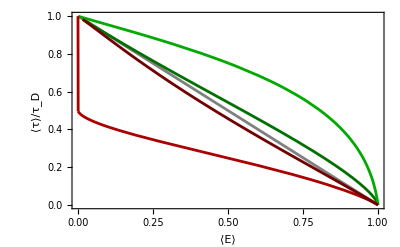

```mathematica
rrmsdye=1/5.4;(*in untis of R0*)
pltE=Show[
Plot[1-e,{e,0,1},PlotStyle->Directive[Gray,AbsoluteThickness[2]]],ParametricPlot[τvsE[pdyeonstick[L,rrmsdye]],{L,0.01,2},PlotRange->All,AspectRatio->1/GoldenRatio,PlotStyle->Directive[Darker@Darker@Green,AbsoluteThickness[2]]],
ParametricPlot[τvsE[Pgc[rrms]],{rrms,0.1,10},PlotRange->All,AspectRatio->1/GoldenRatio,PlotStyle->Directive[Darker@Green,AbsoluteThickness[2]]],
ParametricPlot[τAvsE[Pgc[rrms]],{rrms,0.1,15},PlotRange->{0,1},AspectRatio->1/GoldenRatio,PlotStyle->Directive[Darker@Red,AbsoluteThickness[2]]],ListLinePlot[{{0,1},τAvsE[Pgc[15]]},PlotStyle->Directive[Darker@Red,AbsoluteThickness[2]]],
ParametricPlot[τAvsE[pdyeonstick[L,rrmsdye]],{L,0.01,2},PlotRange->{0,1},AspectRatio->1/GoldenRatio,PlotStyle->Directive[Darker@Darker@Red,AbsoluteThickness[2]]],

Frame->True,FrameLabel->{"⟨E⟩","⟨τ⟩/τ_D"},FrameStyle->Directive[Thick,FontSize[18]],LabelStyle->{FontFamily->"Helvetica",FontSize->18,FontWeight->Bold}
]
```

```mathematica
Clear[donorlifetimedecay]
donorlifetimedecay[p_,R0_,kD_][dt_?NumericQ]:=NIntegrate[ Exp[-kD(1+(R0/r)^6)dt]p[r],{r,0,∞}]
donorlifetimedecay[p_,R0_,kD_][dt:{_?NumericQ ..}]:=ParallelMap[donorlifetimedecay[p,R0,kD],dt]
```

```mathematica
Clear[acceptorlifetimedecay]
acceptorlifetimedecay[p_,R0_,kD_,kA_][dt_?NumericQ]:=NIntegrate[( Exp[-kA dt]-Exp[-kD(1+(R0/r)^6)dt])p[r],{r,0,∞}]
acceptorlifetimedecay[p_,R0_,kD_,kA_][dt:{_?NumericQ ..}]:=ParallelMap[acceptorlifetimedecay[p,R0,kD,kA],dt]
```

```mathematica
FGetRrms[Emean_,p_,R0_]:=Module[{e,rrms},
e[rrms_?NumericQ]:=NIntegrate[1/(1+(r/R0)^6)p[rrms][r],{r,0,∞}];
rrms/.FindRoot[Emean-e[rrms],{rrms,R0}]]
```

```mathematica
FGetL[Emean_,R0_,rrms_]:=Module[{e,L},
e[L_?NumericQ]:=NIntegrate[1/(1+(r/R0)^6)pdyeonstick[L,rrms][r],{r,0,∞}];
L/.FindRoot[Emean-e[L],{L,R0}]]
```

```mathematica
FGetL[0.8,5.4,1]
```

4.11127

```mathematica
tau[kD_][r_]:=1/kD(1/(1+(1/r)^6))
```

```mathematica
Ef[r_]:=(1/(1+(1/r)^-6))
```

```mathematica
r0:=5.4
```

```mathematica
Clear[dgc,agc]
dgc[kd_,e_][times_]:=Module[{decay,rrms=FGetRrms[e,Pgc,r0]},decay=FGCDonorLifeTimeDecay[times,r0,kd,rrms];decay[[All]]/=Total[decay[[All]]];decay];
agc[kd_,ka_,e_][times_]:=Module[{decay,rrms=FGetRrms[e,Pgc,r0]},decay=FGCAcceptorLifeTimeDecay[times,r0,kd,ka,rrms];decay[[All]]/=Total[decay[[All]]];decay];
```

```mathematica
Solve[rss==rf/(1+krot/kdye),krot]
```

{{krot→(kdye (rf-rss))/rss}}

```mathematica
r1[r0_,rss_,kdye_][t_]:=If[rss>0,r0 Exp[-(kdye (r0-rss))/rss t],0 t]
```

```mathematica
GetAnisodecays[f_,r_,L1_,L2_][t_]:={f[t](1+(2-3L1)r[t]),f[t](1-(1-3L2)r[t])}
```

```mathematica
norm[dat_]:=Module[{tot=Total[dat]},If[tot>0.,dat/tot,dat]]
norm2[dat_]:=Module[{tot=Total[dat],tmp},If[tot>0.,dat/tot,(ConstantArray[1./Length[dat],Length[dat]])]
]
```

#### Fluorescence decays

```mathematica
kD=0.25;kA=0.25; rf=0.4;L1=0.;L2=0.;
rrmsdye=1;
Lbound=FGetL[ebound,r0,rrmsdye]
times=Range[0,50,0.016];
{idonlyp,idonlys}=norm/@GetAnisodecays[dstatic[kD],r1[rf,rDfree,kD],L1,L2][times];
{iddp,idds}=norm/@GetAnisodecays[dgc[kD,efree],r1[rf,rDfree,kD],L1,L2][times];
{idap,idas}=norm/@GetAnisodecays[agc[kD,kA,efree],r1[rf,0,kA],L1,L2][times];
{idirap,idiras}=norm/@GetAnisodecays[dstatic[kA],r1[rf,rAfree,kA],L1,L2][times];
{iaap,iaas}=norm/@(RotateRight[#,1500]&)/@GetAnisodecays[dstatic[kA],r1[rf,rAfree,kA],L1,L2][times];
freedecays=Map[conv[norm2[#]]&,GetSubpopDecays[{ntotfree,efree,rDfree,rAfree,α,pieγ},{idap,iddp,idas,idds,idirap,idiras,idonlyp,idonlys},{iaap,iaas}],{2}];

{idonlyp,idonlys}=norm/@GetAnisodecays[dstatic[kD],r1[rf,rDbound,kD],L1,L2][times];
{iddp,idds}=norm/@GetAnisodecays[donorlifetimedecay[pdyeonstick[Lbound,1],r0,kD],r1[rf,rDbound,kD],L1,L2][times];
{idap,idas}=norm/@GetAnisodecays[acceptorlifetimedecay[pdyeonstick[Lbound,1],r0,kD,kA],r1[rf,0,kA],L1,L2][times];
{idirap,idiras}=norm/@GetAnisodecays[dstatic[kA],r1[rf,rAbound,kA],L1,L2][times];
{iaap,iaas}=norm/@(RotateRight[#,1500]&)/@GetAnisodecays[dstatic[kA],r1[rf,rAbound,kA],L1,L2][times];
bounddecays=Map[conv[norm2[#]]&,GetSubpopDecays[{ntotbound,ebound,rDbound,rAbound,α,pieγ},{idap,iddp,idas,idds,idirap,idiras,idonlyp,idonlys},{iaap,iaas}],{2}];
```

4.11127

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

#### Graphs

```mathematica
ListLinePlot[freedecays[[1]],PlotLegends->{1,2,3,4},PlotRange->All]
ListLinePlot[bounddecays[[1]],PlotLegends->{1,2,3,4},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[freedecays[[2]],PlotLegends->{1,2,3,4},PlotRange->All]
ListLinePlot[bounddecays[[2]],PlotLegends->{1,2,3,4},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[freedecays[[3]],PlotLegends->{1,2,3,4},PlotRange->All]
ListLinePlot[bounddecays[[3]],PlotLegends->{1,2,3,4},PlotRange->All]
```

-Graphics-

-Graphics-

#### Background decays

```mathematica
bg=Total/@Partition[irfraw[[All,2]],4];
bg=bg[[1;;Length[times]]]+100000;
bg/=Total[bg];
bg1=bg+1/pieγ*RotateRight[bg,1500];
bg2=bg;
ListPlot[{bg1,bg2},PlotRange->All]
```

-Graphics-

```mathematica
20/0.016
```

1250.

```mathematica
ListPlot[{Range[1250]0.016,bg2[[1;;1250]]}ᵀ,PlotRange->All]
```

-Graphics-

```mathematica
tmeanBgD=Total[bg2[[1;;1250]](Range[1250])0.016]/Total[bg2[[1;;1250]]]
```

9.58239

```mathematica
tmeanBgD=Total[bg2[[1;;1500]](Range[1500])0.016]/Total[bg2[[1;;1500]]]
```

11.5652

#### Simulate

```mathematica
decays={freedecays[[1]],freedecays[[2]],bounddecays[[2]],bounddecays[[3]]};
```

```mathematica
AbsoluteTiming@FTSSimulateTTTRLifeTimes[{nbgA,nbgD,nbgA,nbgD},rmax,w0,w0,{decays},{bg1,bg2,bg1,bg2}]
```

{21.1754,1}

```mathematica
(*FSaveAsHT3["Simulation example 5.ht3"]*)
```

1

```mathematica
FOpenTTTR["Simulation example 5.ht3"]
```

### Analysis

#### PIE Settings and burst identification

```mathematica
FSetRCM[rcm];
FSetDirectAcceptorExcitation[α];
FEnablePie[True];
FSetPIEGamma[pieγ];
FSetFRETRoutes[{"A","D","A","D"}];
FSetAnisotropyRoutes[{"P","P","S","S"},{"P","P","S","S"}]
FSetAnisotropyL1[0];
FSetAnisotropyL2[0];
FSetPIERoutes[FGetAcceptorRoutes[]];
FSetChannelConstraints[chmain={1,1500}];
FSetPIEChannelConstraints[chpie={1500,3000}];
```

```mathematica
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,20,10000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold];
FDetermineBackground[];
bgdecays=FLifeTimeHisto[FRoutes->{1,2,3,4},FPhotonData->FNonBursts  (*Default*),FOutput->FData];
bgrates=FDetermineBackground[]
FDetermineBackground[]
FFindBurstsDeltaT[0.00015,50,10000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold]
FFindBurstsDeltaT[0.00015,80,10000,FPIEBurstIdentificationMethod->FMainChannelOrPieChannelAboveThreshold]
```

{1481.56,1356.5,1501.4,1298.65,0.,0.}

{793.469,787.505,796.564,782.19,0.,0.}

{793.469,787.505,796.564,782.19,0.,0.}

7280

5572

```mathematica
FLifeTimeHisto[FRoutes->{1,2,3,4},FPhotonData->All]
FLifeTimeHisto[FRoutes->{1,2,3,4},FPhotonData->FBursts  (*Default*)]
```

-Graphics-

-Graphics-

#### S vs.E plot

```mathematica
FParamHisto2D["Epie","Spie",{-0.2,1.2,.03},{-0.1,1.2,0.1},PlotRange->{0,200},Contours->40,ColorFunction->(If[#≠0,Hue[(0.73-.73#)],Hue[0.72]]&)]
```

-Graphics-

| Related Guides
▪Fretica

| Related Tech Notes
▪Technical details on TTTR Simulations